```mathematica
moves={{1,2},{2,1},{1,-2},{2,-1},{-1,2},{-2,1},{-1,-2},{-2,-1}};
```

```mathematica
cannon[L1_,L2_]:=Sort[{L1,L2}][[1]]
```

```mathematica
pic[L_]:=Style[Graphics[{
Table[Line[{{0,i},{width,i}}],{i,0,height}],Table[Line[{{i,0},{i,height}}],{i,0,width}],Red,AbsoluteThickness[2],Line[Map[#-{1/2,1/2}&,L]]
},ImageSize->20{width,height}+1,PlotRange->{{-.05,width+.05},{-.05,height+.05}}],Antialiasing->False]
```

```mathematica
probpic[L_]:=Style[Graphics[{LightGreen, Map[Rectangle[#-{1,1},#]&,L],Black,
Table[Line[{{0,i},{width,i}}],{i,0,height}],Table[Line[{{i,0},{i,height}}],{i,0,width}]
},ImageSize->20{width,height}+1],Antialiasing->False]
```

```mathematica
bbi[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=(Max[Min[x1,x2],Min[x3,x4]]<Min[Max[x1,x2],Max[x3,x4]])&&(Max[Min[y1,y2],Min[y3,y4]]<Min[Max[y1,y2],Max[y3,y4]])
```

```mathematica
det[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=Det[{{x1,y1,1},{x2,y2,1},{x3,y3,1}}]
```

```mathematica
inter[{{x1_,y1_},{x2_,y2_}},{{x3_,y3_},{x4_,y4_}}]:=(det[{x1,y1},{x2,y2},{x3,y3}]det[{x1,y1},{x2,y2},{x4,y4}]<0)&&(det[{x3,y3},{x4,y4},{x1,y1}]det[{x3,y3},{x4,y4},{x2,y2}]<0)&&bbi[{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
```

```mathematica
intersect[L_]:=Apply[Or,Map[inter[#[[1]],#[[2]]]&,Flatten[Outer[List,Partition[L,2,1],Partition[L,2,1],1],1]]]
```

```mathematica
solns55=solns;
```

```mathematica
Length[solns55]
```

71

```mathematica
solns64=solns;
```

```mathematica
Length[solns64]
```

34

```mathematica
solns74=solns;
```

```mathematica
Length[solns74]
```

88

```mathematica
solns65=solns;
```

```mathematica
Length[solns65]
```

252

```mathematica
solns66=solns;
```

```mathematica
Length[solns66]
```

1538

```mathematica
solns75=solns;
```

```mathematica
Length[solns75]
```

916

```mathematica
solns85=solns;
```

```mathematica
Length[solns85]
```

3218

```mathematica
solns76=solns;
```

```mathematica
Length[solns76]
```

```mathematica
width=5;
height=5;
solns={};stack=Map[{#}&,Flatten[Table[{i,j},{i,1,width},{j,1,height}],1]];
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
If[First[cur]==Last[cur]&&Length[cur]>3,If[cannon[cur[[2]],cur[[-2]]]==cur[[2]],AppendTo[solns,cur]],If[First[cur]=!=Last[cur]||(First[cur]==Last[cur]&&Length[cur])<2,
poss=Map[Last[cur]+#&,moves];
poss=Select[poss,1≤#[[1]]≤width&&1≤#[[2]]≤height&];
poss=Complement[poss,Rest[cur]];
poss=Select[poss,cannon[First[cur],#]==First[cur]&];
poss=Select[poss,Not[intersect[cur~Join~{#}]]&];
stack=stack~Join~Map[cur~Join~{#}&,poss];
]]]
```

```mathematica
status[L_,pt_]:=If[MemberQ[L,pt],1,Mod[Count[Map[inter[{pt,{1,100}},#]&,Partition[L,2,1]],True],2]+2]
```

```mathematica
stats[L_,M_]:=Sort[Map[status[L,#]&,M]]
```

```mathematica
unique[L_]:=Select[L,Count[L,#]==1&]
```

```mathematica
rw:=RandomInteger[{1,width}]
rh:=RandomInteger[{1,height}]
```

```mathematica
st[L_]:=Table[Count[Transpose[Rest[L]][[1]],k],{k,1,width}]~Join~Table[Count[Transpose[Rest[L]][[2]],k],{k,1,width}]
```

```mathematica
done={};
While[0=!=1,
r1=r2=r3=r4=r5=r6=r7=r8=r9={1,1};
rr={r1,r2,r3,r4,r5,r6,r7,r8,r9};
While[Length[Union[rr]]<9||Length[Intersection[rr,Flatten[Table[{ii,jj},{ii,2,width-1},{jj,2,height-1}],1]]]<4,
r1={rw,rh};
r2={rw,rh};
r3={rw,rh};
r4={rw,rh};
r5={rw,rh};
r6={rw,rh};
r7={rw,rh};
r8={rw,rh};
r9={rw,rh};
rr={r1,r2,r3,r4,r5,r6,r7,r8,r9}];
u=Select[solns,stats[#,rr]=={1,1,1,2,2,2,3,3,3}&];
If[Length[u]==1&&Not[MemberQ[done,Position[solns,u[[1]]][[1,1]]]],
AppendTo[done,Position[solns,u[[1]]][[1,1]]];
Print[probpic[rr]];
Print[pic[u[[1]]]]]]
```

```mathematica
beforepic[L_]:=Style[Graphics[{
MapIndexed[If[#2[[1]]<=width,Text[Style[#1,FontSize->12],{#2[[1]]-1/2,-1/2}],Text[Style[#1,FontSize->12],{width+1/2,#2[[1]]-width-1/2}]]&,L],Black,
Table[Line[{{0,i},{width,i}}],{i,0,height}],Table[Line[{{i,0},{i,height}}],{i,0,width}]
},ImageSize->20{width+1,height+1},PlotRange->{{-.01,width+1.01},{-1.01,height+.01}}],Antialiasing->False]
```

```mathematica
dog=Map[st,solns];
undog=Union[dog];
cat=Select[undog,Count[dog,#]==1&];
uncat=Select[solns,MemberQ[cat,st[#]]&];
uncat=Select[uncat,Extract[st[#],{{1},{width},{width+1},{width+height}}]~Intersection~{0}=={}&];
```

```mathematica
Length[uncat]
```

314

```mathematica
For[kk=1,kk≤Length[uncat],kk++,
Print[beforepic[st[uncat[[kk]]]]];Print[pic[uncat[[kk]]]]]
```

```mathematica
dist[x_,y_]:=(x-y).(x-y)
```

```mathematica
ddist[x_,L_]:=Map[dist[x,#]&,L]
```

```mathematica
findgroup[L_]:=Select[er,MemberQ[#,L]&]
```

```mathematica
prepic[L_]:=Module[{ii,jj,G2,G3},
G2=Table[If[Position[er,{ii,jj}][[1,1]]=!=Position[er,{ii+1,jj}][[1,1]],
              Line[{{ii,jj-1},{ii,jj}}],{}],{ii,1,width-1},{jj,1,
                    height}];
G3=Table[If[Position[er,{ii,jj}][[1,1]]=!=Position[er,{ii,jj+1}][[1,1]],Line[{{ii-1,jj},{ii,jj}}],{}],{ii,1,
             width},{jj,1,height-1}];
Style[Graphics[Flatten[{Thickness[.001],Table[Line[{{i,0},{i,height}}],{i,0,width}],Table[Line[{{0,i},{width,i}}],{i,0,height}],AbsoluteThickness[2],G2,G3,Line[{{0,0},{width,0},{width,height},{0,height},{0,0}}]}],AspectRatio->Automatic,ImageSize->{20width+1,20height+1},PlotRange->{{-.05,width+.05},{-.05,height+.05}}],Antialiasing->False]
    ]
```

```mathematica
pic[L_]:=Module[{ii,jj,G2,G3},
G2=Table[If[Position[er,{ii,jj}][[1,1]]=!=Position[er,{ii+1,jj}][[1,1]],
              Line[{{ii,jj-1},{ii,jj}}],{}],{ii,1,width-1},{jj,1,
                    height}];
G3=Table[If[Position[er,{ii,jj}][[1,1]]=!=Position[er,{ii,jj+1}][[1,1]],Line[{{ii-1,jj},{ii,jj}}],{}],{ii,1,
             width},{jj,1,height-1}];
Style[Graphics[Flatten[{Map[{Hue[.5,1/3],Rectangle[#-1,#]}&,L],Black,Thickness[.001],Table[Line[{{i,0},{i,height}}],{i,0,width}],Table[Line[{{0,i},{width,i}}],{i,0,height}],AbsoluteThickness[2],G2,G3,Line[{{0,0},{width,0},{width,height},{0,height},{0,0}}],Red,AbsoluteThickness[1.5],Line[Map[#-{1/2,1/2}&,L]]
}],AspectRatio->Automatic,ImageSize->{20width+1,20height+1},PlotRange->{{-.05,width+.05},{-.05,height+.05}}],Antialiasing->False]
    ]
```

```mathematica
width=6;
height=6;
solns={};stack=Map[{#}&,Flatten[Table[{i,j},{i,1,width},{j,1,height}],1]];
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
If[First[cur]==Last[cur]&&Length[cur]>3,If[cannon[cur[[2]],cur[[-2]]]==cur[[2]],AppendTo[solns,cur]],If[First[cur]=!=Last[cur]||(First[cur]==Last[cur]&&Length[cur])<2,
poss=Map[Last[cur]+#&,moves];
poss=Select[poss,1≤#[[1]]≤width&&1≤#[[2]]≤height&];
poss=Complement[poss,Rest[cur]];
poss=Select[poss,cannon[First[cur],#]==First[cur]&];
poss=Select[poss,Not[intersect[cur~Join~{#}]]&];
stack=stack~Join~Map[cur~Join~{#}&,poss];
]]]
```

```mathematica
possible=Flatten[Table[{i,j},{i,1,width},{j,1,height}],1];
For[tt=1,tt>0,tt++,
so=solns[[RandomInteger[{1,Length[solns]}]]];
If[Length[so]==13,
er=Map[{#}&,Rest[so]];
fer=Flatten[er,1];
While[Length[fer]<width*height,
oneaway=Select[Complement[possible,fer],Min[ddist[#,fer]]==1&];
next=oneaway[[RandomInteger[{1,Length[oneaway]}]]];
group=Select[fer,dist[next,#]==1&];
m=Flatten[Map[findgroup,group],1];
m1=Min[Map[Length,m]];
group=Select[group,Length[Flatten[findgroup[#],1]]==m1&];piece=group[[RandomInteger[{1,Length[group]}]]];
place=Position[er,piece][[1,1]];
er=Insert[er,next,{place,1}];
fer=Flatten[er,1]];
numsol=Length[Select[Map[Table[Length[Intersection[er[[k]],Rest[#]]],{k,1,Length[er]}]&,solns],Union[#]=={1}&]];
If[numsol==1,If[Union[Map[Length,er]]=={3}||Union[Map[Length,er]]=={3,4}||Union[Map[Length,er]]=={2,3},Print[prepic[er]];Print[pic[so]]]]]]
```

## good ones 65

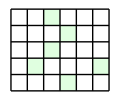

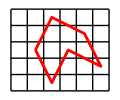

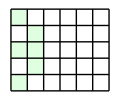

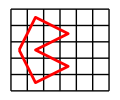

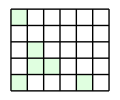

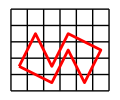

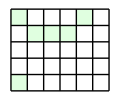

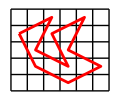

## good ones 74

-Graphics-

-Graphics-

-Graphics-

«33 more identical outputs»

## good ones 55

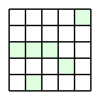

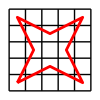

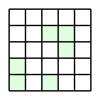

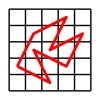

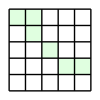

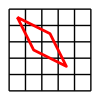

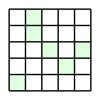

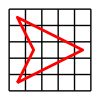

## good ones 6x6

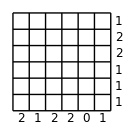

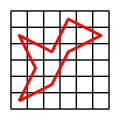

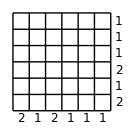

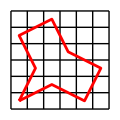

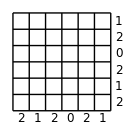

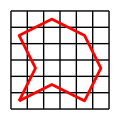

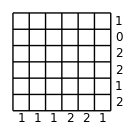

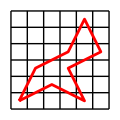

-Graphics-

-Graphics-

-Graphics-

«117 more identical outputs»

## good ones 7x5

-Graphics-

-Graphics-

-Graphics-

«215 more identical outputs»

## good ones 8x5

-Graphics-

-Graphics-

-Graphics-

«625 more identical outputs»

## best ones 5x5

-Graphics-

-Graphics-

-Graphics-

«351 more identical outputs»

## best ones 6x5

-Graphics-

-Graphics-

-Graphics-

«273 more identical outputs»

## best ones 6x6

-Graphics-

-Graphics-

-Graphics-

«313 more identical outputs»

## best ones 6x6 perfect

-Graphics-

-Graphics-

-Graphics-

«43 more identical outputs»

## best ones 7x6

-Graphics-

-Graphics-

-Graphics-

«1013 more identical outputs»

## best ones 7x6 perfect

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»